### Signal Generation

```mathematica
f:=10
```

```mathematica
fs:=500
```

```mathematica
samples:=500
```

```mathematica
runTime=1/fs*samples//N
```

1.

```mathematica
InSignal:=Table[Sin[2π*f*t],{t,0,runTime,1/fs}]
```

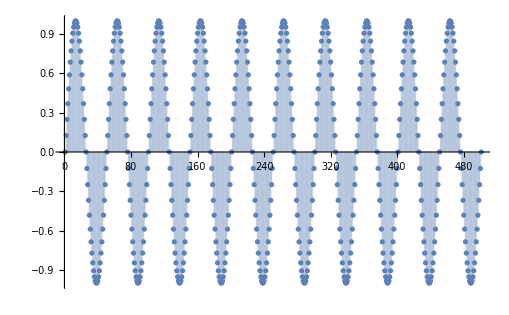

```mathematica
ListPlot[InSignal, Filling->Axis]
```

```mathematica
scaleF:= 2^15*.8
```

```mathematica
stim:=Round[InSignal*scaleF]
```

```mathematica
new:=TableForm[stim]
```

```mathematica
Export["stim_in.txt",new, "Table"]
```

stim_in.txt

### Output

```mathematica
out:=Import["output.txt","Table"]
```

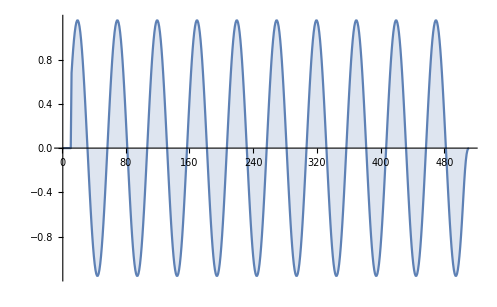

```mathematica
DiscretePlot[Part[out,n]/scaleF,{n,1,Length[out]}]
```